### Plot comparing kernel with/without full angular dependence

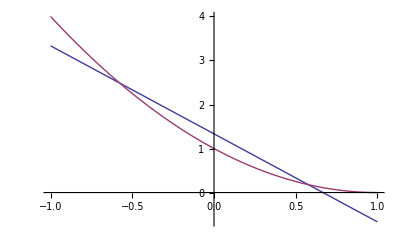

```mathematica
Plot[{
4/3 - 2*μ,
4/3 - 2*μ+2/3*1/2*(3μ^2-1)
},{μ,-1,1}]
```

### Evaluate phi_l

```mathematica
phil[l_,ωa_,ωb_,Ee_]:=Module[{y,AA,BB,CC,DD,μ0,f,integrand,musub,xsub,dmudx,a,b,c,d,tmp0,tmp1,tmp2,μ,x,J1,J2,phi},

(* Equations C57-C61 and text above C66 *)
y=(ωb^2 ωa^2 (1-μ)^2)/(ωb^2+ωa^2+2ωa ωb μ)^(5/2);
AA=ωb^2 y ((ωb+ωa μ)^2-1/2 ωa^2 (1-μ^2));
BB=ωb y(-2ωb^2+ωa^2+3ωa ωb-ωa ωb μ+3ωa^2 μ);
CC=y(ωb^2+ωa^2-3ωa ωb - ωa ωb μ);
DD=4Ee^2ωa^2(1-μ^2)ωa ωb(1-μ)(-2Ee^2+2Ee(ωa+ωb)-ωa ωb(1-μ));
μ0=1-2Ee(ωa+ωb-Ee)/(ωa ωb);
f=(AA+BB Ee+CC Ee^2)LegendreP[l,μ];

(* Substitutions to make the integral easier - one is inverse of the other *)
musub = (x^2 - ωb^2 - ωa^2)/(2 ωb ωa);
xsub = Sqrt[ωb^2 + ωa^2 + 2 ωb ωa μ];
dmudx=D[musub,x];

(* Evaluate the integral and get the coefficients for the heaviside functions *)
tmp0=Simplify[FullSimplify[f]/.μ->musub,x>0];
tmp1=Normal[Series[Expand[dmudx tmp0],{x,0,100}]];
tmp2=Simplify[Integrate[tmp1,x]/.x->xsub];
a=Simplify[(tmp2/.μ->1) - (tmp2/.μ->μ0),{ωa>0,ωb>0,Ee>0,ωb>ωa>Ee}];
b=Simplify[(tmp2/.μ->1) - (tmp2/.μ->μ0),{ωa>0,ωb>0,Ee>0,Ee>ωa>ωb}];
c=Simplify[(tmp2/.μ->1) - (tmp2/.μ->-1),{ωa>0,ωb>0,Ee>0,ωb>Ee>ωa}];
d=Simplify[(tmp2/.μ->1) - (tmp2/.μ->-1),{ωa>0,ωb>0,Ee>0,ωa>Ee>ωb}];

(* Define the J's *)
J1=(1/(ωb ωa)HeavisideTheta[ωa+ωb-Ee]*(a(HeavisideTheta[ωa-Ee]HeavisideTheta[ωb-ωa]+HeavisideTheta[ωb-Ee]HeavisideTheta[ωa-ωb])+ b(HeavisideTheta[Ee-ωa]HeavisideTheta[ωa-ωb]+ HeavisideTheta[Ee-ωb]HeavisideTheta[ωb-ωa])+c(HeavisideTheta[Ee-ωa]HeavisideTheta[ωb-Ee])+d(HeavisideTheta[Ee-ωb]HeavisideTheta[ωa-Ee])
));
J2=J1/.ωb->asdf/.ωa->ωb/.asdf->ωa;

(* And finally we have phi *)
phi=Simplify[(CV+CA)^2 J1+(CV-CA)^2 J2]
]
```

### Evaluate phi^a_l,TP

Define the electron thermal distribution

```mathematica
mue=0;
kT=Infinity;
F[E_,mu_,kT_]:=1/(Exp[(E-mu)/kT]+1)
```

Integrate the phi’s over energy and the electron/positron distributions

```mathematica
philTP[l_,ωa_,ωb_]:=Simplify[Assuming[{ωa>0,ωb>0},Integrate[
2 G^2/(2Pi)phil[l,ωa,ωb,Ee](1-F[Ee,mue,kT])(1-F[ωa+ωb-Ee,-mue,kT])
,{Ee,0,ωb+ωa}]],ωb>ωa]
phi0TP=philTP[0,ωa,ωb]
phi1TP=philTP[1,ωa,ωb]
phi2TP=philTP[2,ωa,ωb]
(* phi3TP=philTP[3,ωa,ωb] *)
```

(4 (CA^2+CV^2) G^2 ωa ωb)/(9 π)

-(2 (CA^2+CV^2) G^2 ωa ωb)/(9 π)

(2 (CA^2+CV^2) G^2 ωa ωb)/(45 π)

0

### Combine terms to get R

```mathematica
coeff[n_]:=(2n+1)/2
R=Simplify[coeff[0]phi0TP LegendreP[0,cosTheta]+
coeff[1]phi1TP LegendreP[1,cosTheta]+
coeff[2]phi2TP LegendreP[2,cosTheta]+
coeff[3]phi3TP LegendreP[3,cosTheta]]
```

((-1+cosTheta)^2 (CA^2+CV^2) G^2 ωa ωb)/(6 π)

### Check units

```mathematica
IntegrandRuffert=(1/4) σ0 c/((me c^2)^2 (h c)^6)C12/3 (1-cosTheta)^2 fa fb ωa^3 ωb^3(ωa+ωb);
IntegrandBruenn=R ωa^2 ωb^2(ωa+ωb) fa fb (h c)^-6;
constantreps={
sin2thetaw->0.23,
c->2.99792458*10^10 ,(* cm/s *)
σ0->1.76*10^-44, (*cm^2*)
me->9.1093897*10^-28 (*g*),
h->6.6260755*10^-27, (* erg s *)
MeVtoErg->1.60217662*10^-6 (* erg/MeV *)
};
weakreps={
CV->1/2,
CA->1/2+2 sin2thetaw
};
BruennReps={G->Sqrt[1.55*10^-33 * (1.60217662*10^-6)^-2] (* sqrt(cm^3 erg^-2 s^-1) *)};
RuffertReps={C12->(CV-CA)^2+(CV+CA)^2};
Simplify[IntegrandRuffert/.RuffertReps/.weakreps/.constantreps]
Simplify[IntegrandBruenn/.BruennReps/.weakreps/.constantreps]
%/%%
```

2.50171×10^72 (-1.+cosTheta)^2 fa fb ωa^3 ωb^3 (ωa+ωb)

6.10839×10^71 (-1.+cosTheta)^2 fa fb ωa^3 ωb^3 (ωa+ωb)

0.244168

```mathematica
Sqrt[G^2*(h c/(2 Pi))^4]/.BruennReps/.constantreps
```

2.45612×10^-44

```mathematica
2*(CV^2+CA^2)/.weakreps/.constantreps
```

2.3432

```mathematica
σ0 c Pi/(4 (me c^2)^2)/.constantreps
G^2/.BruennReps
```

6.18247×10^-22

6.03825×10^-22

```mathematica
6.182468000332461*^-22*(1.60217662*10^-6)^2
```

1.58702×10^-33

```mathematica
GF2=σ0 Pi (h c/(2 Pi))^4/(4 (me c^2)^2)/.constantreps
GF2/(c (h c/(2 Pi))^2)*(MeVtoErg^-2)/.constantreps
```

2.0603×10^-98

2.67852×10^-64

```mathematica
c (h c/(2 Pi))^2/.constantreps
```

2.99651×10^-23

### Check whether there is extra angular dependence

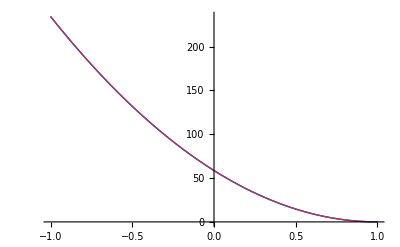

58.58

3.55271×10^-14

```mathematica
moments[x_]:=1/2 tmp0 + 3/2 tmp1 x + 5/2 tmp2 1/2(3 x^2-1)
explicit[x_]:=1/2*3/4tmp0(1-x)^2
Plot[{moments[x],explicit[x]},{x,-1,1}]
explicit[0]
moments[0]-explicit[0]
```

### Angular Integral Assuming Isotropy

```mathematica
CosTheta[μa_,μb_,ϕa_,ϕb_]:=μa μb + Sqrt[(1-μa^2)(1-μb^2)]Cos[ϕb-ϕa]
Integrate[Integrate[Integrate[Integrate[
(1-CosTheta[μa,μb,ϕa,ϕb])^2
,{ϕa,0,2Pi}],{ϕb,0,2Pi}],{μa,-1,1}],{μb,-1,1}]
```

(64 π^2)/3

## Energy Integral Bounds

The collision must obey energy and momentum conservation. Naievely using only energy conservation says the two neutrinos must have at least enough energy to make two electrons, but there is also angular dependence. Momentum conservation means the resulting leptons will necessarily have some kinetic energy, which increases the minimum energy of the neutrinos to annihilate.

```mathematica
Simplify[Solve[{
p1 Cos[θ1] + p2 Cos[θ-θ1]==2Ee/c,
p1 Sin[θ1]==p2 Sin[θ-θ1]
},Ee,{θ1}]]
FullSimplify[
(p1+p2)^2c^2>4(Ee^2+m^2c^4)
/.%[[1]][[1]],c>0]
FullSimplify[%/.m->0,Cos[θ]≤1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{Ee→-1/2 c √(p1^2+p2^2+2 p1 p2 Cos[θ])},{Ee→1/2 c √(p1^2+p2^2+2 p1 p2 Cos[θ])}}

p1 p2>2 c^2 m^2+p1 p2 Cos[θ]

p1 p2>p1 p2 Cos[θ]